```mathematica
u[x_,t_]:=(x+t)^3
Plot3D[u[x,t],{x,0,1},{t,0,10},BoxRatios->{1, 1, 1}]
```

-Graphics3D-

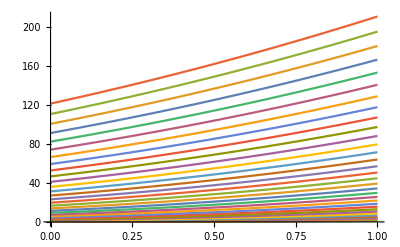

```mathematica
(*Here are some time snapshots of the solution*)
myPlotTable:=Table[u[x,t],{t,0,5,.15}]
Plot[myPlotTable,{x,0,1}]
```